## 半人马座

```mathematica
M=1.99 10^30;AU=1.5 10^11;R1=6AU;R2=5.5 AU;R3=13000AU;m1=1.08M;m2=0.91M;m3=0.12M;
G=6.67 10^-11;ye=100*365 24 3600;alpha=2;
```

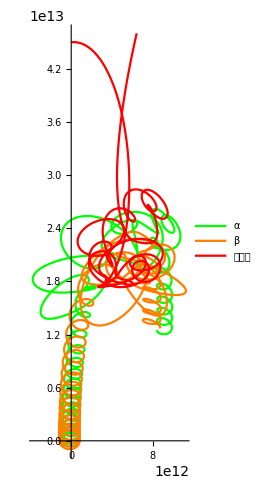

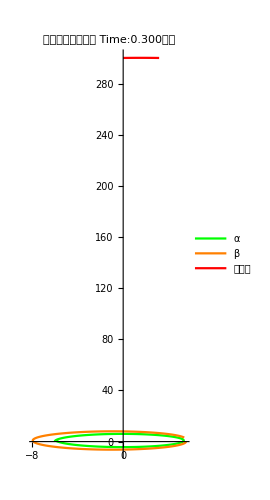
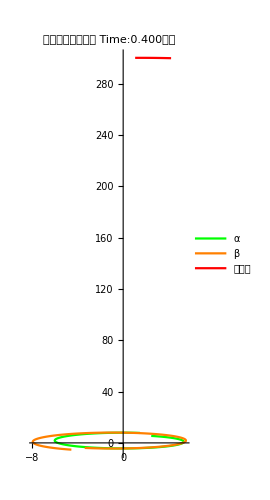
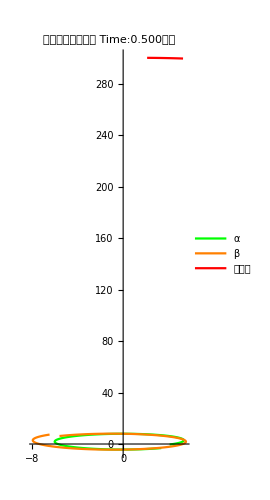
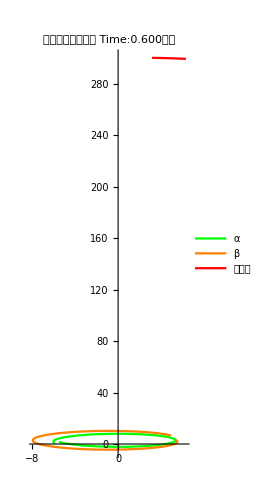
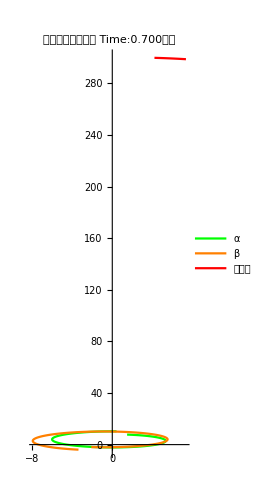
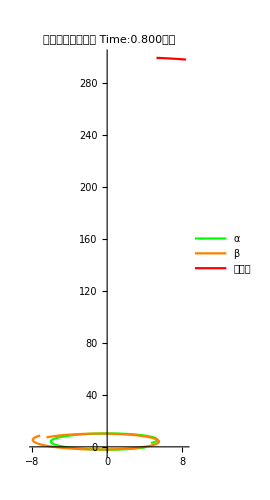
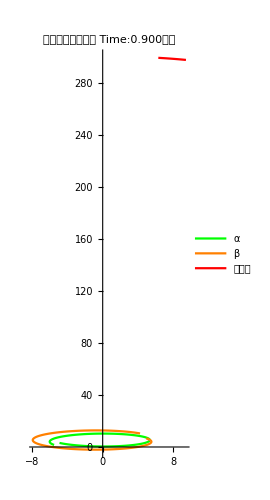
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

$Aborted

```mathematica
Module[{x1,x2,x3,y1,y2,y3,tt},tt=15;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==-R1,x1'[0]==0,y1[0]==0,y1'[0]==6100,x2[0]==R2,x2'[0]==0,y2[0]==0,y2'[0]==-6700,x3[0]==0,x3'[0]==500,y3[0]==50R1,y3'[0]==60},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}},{t,0,tt ye },PlotStyle->{Green,Orange,Red},PlotLegends->{"α","β","比邻星"}]];
s=Table[Show[ParametricPlot[{{x1[τ]/AU,y1[τ]/AU},{x2[τ]/AU,y2[τ]/AU},{x3[τ]/AU,y3[τ]/AU}},{τ,(t-0.3) ye,t ye},PlotStyle->{Green,Orange,Red},PlotLegends->{"α","β","比邻星"},PlotLabel->"半人马座三星系统\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"世纪"],Graphics[{Green,PointSize[Large],Point[{x1[t ye],y1[t ye]}],Orange,PointSize[Large],Point[{x2[t ye],y2[t ye]}],Red,PointSize[Large],Point[{x3[t ye],y3[t ye]}]}]],{t,0.3,tt,0.1}];
Print[s];
Export["threebody.gif",s,"DisplayDurations"->0.06]]
```

```mathematica
SystemOpen["threebody.gif"]
```

```mathematica
SystemOpen["threebody.gif"]
```

```mathematica
SystemOpen["threebody.gif"]
```

## 一个拓展问题：如果万有引力不平方反比怎么办？这里保持天体在现实世界的初始条件做个实验

```mathematica
R1=1.5 10^11;R2=2.3 10^11;m1=5.965 10^24;m2=6.4 10^23;(*1是地球2是火星*)
M=1.99 10^30;G0=6.67 10^-11;ye=365 24 3600;
```

```mathematica
alpha=2;ω1=Sqrt[G0 M]/R1^(3/2);ω2=Sqrt[G0 M]/R2^(3/2);G=G0*R1^(alpha-2);
Module[{x1,x2,x3,y1,y2,y3,tt,α},tt=5;α=Pi/10;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==R1,x1'[0]==0,y1[0]==0,y1'[0]==ω1 R1,x2[0]==R2 Cos[α],x2'[0]==-ω2 R2 Sin[α],y2[0]==R2 Sin[α],y2'[0]==ω2 R2 Cos[α],x3[0]==0,x3'[0]==0,y3[0]==0,y3'[0]==0},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x3[t],y3[t]},{x2[t],y2[t]}},{t,0,tt ye },PlotStyle->{Blue,{Orange,Thickness[0.05]},Green},PlotLegends->{"地球","太阳","火星"}]];
a=Table[Show[ParametricPlot[{{x1[τ],y1[τ]},{x3[τ],y3[τ]},{x2[τ],y2[τ]}},{τ,(t-0.05) ye,t ye},PlotStyle->{Blue,Orange,Green},PlotLegends->{"地球","太阳","火星"},PlotLabel->"平方反比\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"Year",PlotRange->1.3 R2],Graphics[{Blue,Point[{x1[t ye],y1[t ye]}],Green,Point[{x2[t ye],y2[t ye]}],Orange,PointSize[Large],Point[{x3[t ye],y3[t ye]}]},PlotRange->1.3R2]],{t,0.05,tt,0.025}];
Print[a];
Export["平方反比3.gif",a,"DisplayDurations"->0.04]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

平方反比3.gif

```mathematica
alpha=3/2;ω1=Sqrt[G0 M]/R1^(3/2);ω2=Sqrt[G0 M]/R2^(3/2);G=G0*R1^(alpha-2);
Module[{x1,x2,x3,y1,y2,y3,tt,α},tt=5;α=Pi/10;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==R1,x1'[0]==0,y1[0]==0,y1'[0]==ω1 R1,x2[0]==R2 Cos[α],x2'[0]==-ω2 R2 Sin[α],y2[0]==R2 Sin[α],y2'[0]==ω2 R2 Cos[α],x3[0]==0,x3'[0]==0,y3[0]==0,y3'[0]==0},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x3[t],y3[t]},{x2[t],y2[t]}},{t,0,tt ye },PlotStyle->{Blue,{Orange,Thickness[0.05]},Green},PlotLegends->{"地球","太阳","火星"}]];
a=Table[Show[ParametricPlot[{{x1[τ],y1[τ]},{x3[τ],y3[τ]},{x2[τ],y2[τ]}},{τ,(t-0.05) ye,t ye},PlotStyle->{Blue,Orange,Green},PlotLegends->{"地球","太阳","火星"},PlotLabel->"3/2次反比\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"Year",PlotRange->1.3 R2],Graphics[{Blue,Point[{x1[t ye],y1[t ye]}],Green,Point[{x2[t ye],y2[t ye]}],Orange,PointSize[Large],Point[{x3[t ye],y3[t ye]}]},PlotRange->1.3R2]],{t,0.05,tt,0.025}];
Print[a];
Export["32反比3.gif",a,"DisplayDurations"->0.04]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

32反比3.gif

```mathematica
alpha=1;ω1=Sqrt[G0 M]/R1^(3/2);ω2=Sqrt[G0 M]/R2^(3/2);G=G0*R1^(alpha-2);
Module[{x1,x2,x3,y1,y2,y3,tt,α},tt=5;α=Pi/10;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==R1,x1'[0]==0,y1[0]==0,y1'[0]==ω1 R1,x2[0]==R2 Cos[α],x2'[0]==-ω2 R2 Sin[α],y2[0]==R2 Sin[α],y2'[0]==ω2 R2 Cos[α],x3[0]==0,x3'[0]==0,y3[0]==0,y3'[0]==0},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x3[t],y3[t]},{x2[t],y2[t]}},{t,0,tt ye },PlotStyle->{Blue,{Orange,Thickness[0.05]},Green},PlotLegends->{"地球","太阳","火星"}]];
a=Table[Show[ParametricPlot[{{x1[τ],y1[τ]},{x3[τ],y3[τ]},{x2[τ],y2[τ]}},{τ,(t-0.05) ye,t ye},PlotStyle->{Blue,Orange,Green},PlotLegends->{"地球","太阳","火星"},PlotLabel->"一次反比\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"Year",PlotRange->1.3 R2],Graphics[{Blue,Point[{x1[t ye],y1[t ye]}],Green,Point[{x2[t ye],y2[t ye]}],Orange,PointSize[Large],Point[{x3[t ye],y3[t ye]}]},PlotRange->1.3R2]],{t,0.05,tt,0.025}];
Print[a];
Export["一次反比3.gif",a,"DisplayDurations"->0.04]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

一次反比3.gif

```mathematica
alpha=-1;ω1=Sqrt[G0 M]/R1^(3/2);ω2=Sqrt[G0 M]/R2^(3/2);G=G0*R1^(alpha-2);
Module[{x1,x2,x3,y1,y2,y3,tt,α},tt=5;α=Pi/10;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==R1,x1'[0]==0,y1[0]==0,y1'[0]==ω1 R1,x2[0]==R2 Cos[α],x2'[0]==-ω2 R2 Sin[α],y2[0]==R2 Sin[α],y2'[0]==ω2 R2 Cos[α],x3[0]==0,x3'[0]==0,y3[0]==0,y3'[0]==0},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x3[t],y3[t]},{x2[t],y2[t]}},{t,0,tt ye },PlotStyle->{Blue,{Orange,Thickness[0.05]},Green},PlotLegends->{"地球","太阳","火星"}]];
a=Table[Show[ParametricPlot[{{x1[τ],y1[τ]},{x3[τ],y3[τ]},{x2[τ],y2[τ]}},{τ,(t-0.05) ye,t ye},PlotStyle->{Blue,Orange,Green},PlotLegends->{"地球","太阳","火星"},PlotLabel->"一次正比\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"Year",PlotRange->1.3 R2],Graphics[{Blue,Point[{x1[t ye],y1[t ye]}],Green,Point[{x2[t ye],y2[t ye]}],Orange,PointSize[Large],Point[{x3[t ye],y3[t ye]}]},PlotRange->1.3R2]],{t,0.05,tt,0.025}];
Print[a];
Export["一次正比3.gif",a,"DisplayDurations"->0.04]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

一次正比3.gif

```mathematica
alpha=-2;ω1=Sqrt[G0 M]/R1^(3/2);ω2=Sqrt[G0 M]/R2^(3/2);G=G0*R1^(alpha-2);
Module[{x1,x2,x3,y1,y2,y3,tt,α},tt=5;α=Pi/10;so1=NDSolve[{x1''[t]==-G ((M (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y1''[t]==-G ((M (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^((alpha+1)/2)+(m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),x2''[t]==-G ((M (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (x2[t]-x1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),y2''[t]==-G ((M (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^((alpha+1)/2)+(m1 (y2[t]-y1[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^((alpha+1)/2)),
x3''[t]==-G ((m1 (x3[t]-x1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (x3[t]-x2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),y3''[t]==-G ((m1 (y3[t]-y1[t]))/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^((alpha+1)/2)+(m2 (y3[t]-y2[t]))/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^((alpha+1)/2)),
x1[0]==R1,x1'[0]==0,y1[0]==0,y1'[0]==ω1 R1,x2[0]==R2 Cos[α],x2'[0]==-ω2 R2 Sin[α],y2[0]==R2 Sin[α],y2'[0]==ω2 R2 Cos[α],x3[0]==0,x3'[0]==0,y3[0]==0,y3'[0]==0},{x1,y1,x2,y2,x3,y3},{t,0,tt ye}];
{x1,y1,x2,y2,x3,y3}={x1,y1,x2,y2,x3,y3}/.so1[[1]];
Print[ParametricPlot[{{x1[t],y1[t]},{x3[t],y3[t]},{x2[t],y2[t]}},{t,0,tt ye },PlotStyle->{Blue,{Orange,Thickness[0.05]},Green},PlotLegends->{"地球","太阳","火星"}]];
a=Table[Show[ParametricPlot[{{x1[τ],y1[τ]},{x3[τ],y3[τ]},{x2[τ],y2[τ]}},{τ,(t-0.05) ye,t ye},PlotStyle->{Blue,Orange,Green},PlotLegends->{"地球","太阳","火星"},PlotLabel->"二次正比\nTime:"<>ToString[NumberForm[t,{Infinity,3}]]<>"Year",PlotRange->1.3 R2],Graphics[{Blue,Point[{x1[t ye],y1[t ye]}],Green,Point[{x2[t ye],y2[t ye]}],Orange,PointSize[Large],Point[{x3[t ye],y3[t ye]}]},PlotRange->1.3R2]],{t,0.05,tt,0.025}];
Print[a];
Export["二次正比3.gif",a,"DisplayDurations"->0.04]]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

二次正比3.gif